### with spoofing

On server, create a file ~/.spoof_14.3.m (for 14.3. being my local license), which contains

Unprotect[$VersionNumber, $Version];
$VersionNumber = 14.3;
$Version = “14.3.0 for Linux x86 (64-bit)”;
Protect[$VersionNumber, $Version];

Here just run:

```mathematica
CloseKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local}

```mathematica
(*Define the custom launch command for the remote 14.2 kernel*)
customCmd="wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit";

(*Configure the kernel object with the spoofed command*)
kernel=KernelConfiguration["ssh://strelda@ipnp36.troja.mff.cuni.cz","KernelCommand"->customCmd];

(*Launch 64 instances of this spoofed remote kernel*)
LaunchKernels[Table[kernel,64]]
```

{strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit,strelda@ipnp36.troja.mff.cuni.cz/wolfram -initfile ~/spoof_14_3.m -wstp -linkmode Connect `4` -linkname `2` -subkernel -noinit}

# Settings

```mathematica
EigensystemSorted[H_,ρ_?NumericQ,ϕ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[H[ρ,ϕ]];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,Map[Normalize,eig]}
]
```

```mathematica
endif[H_,{x_?NumericQ,y_?NumericQ},bottomlevel_]:=Module[{e},
e=Sort@N@Eigenvalues[H[x,y]];
e[[bottomlevel+1]]-e[[bottomlevel]]]
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
(*chevron plot markers*)(*V shape: \/(lower-level DPs)*)vMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,1},{0,0},{1,1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
(* ∧shape: /\  (upper-level DPs)*)uMarker=Graphics[{AbsoluteThickness[2],Line[{{-1,-1},{0,0},{1,-1}}]},PlotRange->{{-1,1},{-1,1}},ImagePadding->0,Background->None];
plus=Graphics[{Line[{{-√2,0},{√2,0}}],Line[{{0,-√2},{0,√2}}]}];
```

```mathematica
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
ResourceFunction["PlotGrid"];
```

```mathematica
MyBlue=RGBColor[0,0.4,1]
MyGreen=RGBColor[0,1,0]
MyRed=RGBColor[1,0,0]
MyViolet=RGBColor[128/255,0,128/255]
geodColor=RGBColor[0,0.7,0.7]
geodThickness=0.015;
infGray=GrayLevel[0.3];
fillGray=GrayLevel[0.92];
blobGray=GrayLevel[0.9];
```

RGBColor[0, 0.4, 1]

RGBColor[0, 1, 0]

RGBColor[1, 0, 0]

RGBColor[Rational[128, 255], 0, Rational[128, 255]]

RGBColor[0, 0.7, 0.7]

# Qutrit in magnetic field

```mathematica
(*Spin-1 matrices*)
Sx=1/Sqrt[2] {{0,1,0},{1,0,1},{0,1,0}};
Sy=1/Sqrt[2] {{0,-I,0},{I,0,-I},{0,I,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};

(*Full spin-1 Hamiltonian with zero-field splitting*)
(*Following NV center convention from [Rondin14]*)
```

```mathematica
HSpinFull[Bx_,By_,Bz_,D_,E_,μB_,g_]:=D*Sz.Sz+E*(Sx.Sx-Sy.Sy)+g μB(Bx*Sx+By*Sy+Bz*Sz)//Simplify
```

```mathematica
Chop@HSpinFull[Bx,By,Bz,d,e,μB,g]//MatrixForm
```

(d+Bz g μB | ((Bx-ⅈ By) g μB)/(√2) | e
((Bx+ⅈ By) g μB)/(√2) | 0 | ((Bx-ⅈ By) g μB)/(√2)
e | ((Bx+ⅈ By) g μB)/(√2) | d-Bz g μB)

```mathematica
H[Bx_,Bz_]:=HSpinFull[Bx,0,Bz,d,e,μB,g] (*multiply by 1000 to use mT as units of B*)
```

#### Exact root finding

```mathematica
ens=Eigenvalues[H[0,y]]
```

{0,d-√(e^2+g^2 y^2 μB^2),d+√(e^2+g^2 y^2 μB^2)}

```mathematica
sol=Quiet@Solve[ens[[1]]==ens[[2]],y]
root=sol[[2]]
```

{{y→-(√(d^2-e^2))/(g μB)},{y→(√(d^2-e^2))/(g μB)}}

{y→(√(d^2-e^2))/(g μB)}

```mathematica
ens/.y->0
```

{0,d-√(e^2),d+√(e^2)}

So the energy gap is 2e.

```mathematica
d=2.87;      (* GHz-zero-field splitting*)
e=0.5;            (* e~100 kHz for high purity chemical vapour deposition grown diamond samples, but we need 0 to get exact crossing*)
μB=14;    (*GHz/T-effective gyromagnetic parameter*)
g=2 ;(*Landé g-factor*)

Chop@H[Bx,Bz]//MatrixForm
endif1[y_?NumericQ]:=Module[{sp},
sp=Sort[Eigenvalues[N@H[0,y]]];
sp[[2]]-sp[[1]]
]
```

(2.87+28 Bz | 14 √2 Bx | 0.5
14 √2 Bx | 0 | 14 √2 Bx
0.5 | 14 √2 Bx | 2.87-28 Bz)

```mathematica
yroot=N[y/.root,43]
```

0.100933

```mathematica
{Bz0,Bz1,Bz2}={0,2yroot,yroot}; (*needed for shifts later*)
```

#### Plots

```mathematica
plot3d=Plot3D[Evaluate[Sort[Eigenvalues[H[Bx,Bz]]]],{Bx,-0.2,0.2},{Bz,-0.2,0.2},PlotPoints->20,AxesLabel->{"B_x","B_z","E"},
PlotStyle->{
Directive[RGBColor[0.,0.2,0.7],Opacity[0.7]],
Directive[RGBColor[0.2,0.5,0.9],Opacity[0.5]],
Directive[RGBColor[0.5,0.7,1],Opacity[0.2]]}]
```

-Graphics3D-

```mathematica
{zMin,zMax}={0,10};
colorMapping=(Blend[{White,Black},Rescale[#,{zMin,zMax}]]&);

optEndif={PlotPoints->10,ColorFunctionScaling->False,ColorFunction->colorMapping,FrameLabel->{"B_x","B_z"}};
```

Energy differences between levels

```mathematica
grid=Quiet@ResourceFunction["PlotGrid"][{{Show[{
DensityPlot[endif[H,{Bx,Bz},2],{Bx,-0.23,0.23},{Bz,-0.23,0.23},Evaluate@optEndif] (*top plot*)
}]},
{Show[{DensityPlot[endif[H,{Bx,Bz},1],{Bx,-0.23,0.23},{Bz,-0.23,0.23},Evaluate@optEndif],(*bottom plot background*)
ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{cross,0.1}],  (*DP1*)
ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{cross,0.1}] (*DP0*)
}]}}]
```

-Graphics-

```mathematica
Sort@Eigenvalues[H[0,Bz0]]
Sort@Eigenvalues[H[0,Bz2]]
Sort@Eigenvalues[H[0,-Bz2]]
```

{0.,2.37,3.37}

{0.,9.94817×10^-17,5.74}

{0.,9.94817×10^-17,5.74}

## Analysis

```mathematica
xyTorϕ={x->r Cos[ϕ],y->r Sin[ϕ]};
H0[r_,ϕ_]=H[x,y]/.{y->y-Bz2}/.xyTorϕ//FullSimplify;(* around dp on M0*)
H1[r_,ϕ_]=H[x,y]/.{y->y+Bz2}/.xyTorϕ//FullSimplify; (* around dp on M0*)
H2[r_,ϕ_]=H[x,y]/.xyTorϕ//FullSimplify; (* around dp on M1*)
```

```mathematica
(*check the r->0 degeneracy*)
Chop@Sort@Eigenvalues@H0[0,ϕ]
Chop@Sort@Eigenvalues@H1[0,ϕ]
Chop@Sort@Eigenvalues@H2[0,ϕ]
```

{0,0,5.74}

{0,0,5.74}

{0,2.37,3.37}

```mathematica
(*conversion from radial to shifted radial, which will be used mainly for geometry*)
r[R_]:=RealSign[R-1/2](R-1/(4R))
ϕ[R_,Φ_]:=UnitStep[R-1/2]Φ+UnitStep[1/2-R](Φ+π)
HASR[H_,R_,Φ_]:=H[r[R],ϕ[R,Φ]]//FullSimplify
```

```mathematica
(*Hamiltonian in three different shifted radial coordinates, around three different DPs*)
HS0[R_?NumericQ,Φ_?NumericQ]:=HASR[H0,R,Φ];
HS1[R_?NumericQ,Φ_?NumericQ]:=HASR[H1,R,Φ];
HS2[R_?NumericQ,Φ_?NumericQ]:=HASR[H2,R,Φ];
```

```mathematica
SRToR[{R_,Φ_}]:={r[R],Mod[ϕ[R,Φ],2π]}(*shifted radial to radial*)
RToSRIn[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (-r+√(1+r^2));
Φ=Mod[ϕ-π,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
RToSROut[{r_,ϕ_}]:=Module[{R,Φ},
R=1/2 (r+√(1+r^2));
Φ=Mod[ϕ,2π];
{R,Φ}
];(*radial to shifted radial, look at Plot[r[R],{R,0,2}] and Solve[r==(R-1/(4R)),R] to see why this works*)
SCToSR[X_,Y_]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
CToR[x_,y_]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)
RToC[r_,φ_]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
(*vector versions*)
SCToSR[{X_,Y_}]:={√(X^2+Y^2),ArcTan[X,Y]}; (*shifted cartesian to shifted radial*)
SRToSC[{R_,Φ_}]:={R Cos[Φ],R Sin[Φ]}; (*shifted radial to shifted cartesian*)
RToC[{r_,φ_}]:={r Cos[φ],r Sin[φ]}; (*shifted radial to shifted cartesian*)
CToR[{x_,y_}]:={√(x^2+y^2),ArcTan[x,y]}; (*shifted radial to shifted cartesian*)

C0ToC1[{x_,y_}]:={x,y-Bz1}
C1ToC0[{x_,y_}]:={x,y+Bz1}
C0ToC2[{x_,y_}]:={x,y-Bz2}
C2ToC0[{x_,y_}]:={x,y+Bz2}
C1ToC2[{x_,y_}]:={x,y+Bz2}
C2ToC1[{x_,y_}]:={x,y-Bz2}
```

## Spectrum in stretched coordinates

```mathematica
sol1=Quiet@Solve[r[R]==Bz1,R]
```

{{R→-0.611018},{R→0.409153},{R→0.611018}}

```mathematica
sol2=Quiet@Solve[r[R]==Bz2,R]
```

{{R→-0.553007},{R→0.452074},{R→0.553007}}

```mathematica
DP1In=R/.sol1[[2]];
DP1Out=R/.sol1[[3]];
DP2In=R/.sol2[[2]];
DP2Out=R/.sol2[[3]];
```

```mathematica
markersize=0.1;
linethickness=0.015;
plotDP0=Show[ParametricPlot[1/2{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{MyBlue,Dashed,Thickness[linethickness]}],ListPlot[{{0,DP1Out}},PlotStyle->MyRed,PlotMarkers->{uMarker,markersize}],
ListPlot[{{0,-DP1In}},PlotStyle->MyRed,PlotMarkers->{vMarker,markersize}]];
plotDP1=Show[ParametricPlot[1/2{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{MyRed,Dashed,Thickness[linethickness]}],
ListPlot[{{0,-DP1Out}},PlotStyle->MyBlue,PlotMarkers->{uMarker,markersize}],
ListPlot[{{0,DP1In}},PlotStyle->MyBlue,PlotMarkers->{vMarker,markersize}]];
plotDPs[hNum_?IntegerQ]:={plotDP0,plotDP1}[[hNum+1]]
```

```mathematica
EnDifSR[H_,R_?NumericQ,Φ_?NumericQ,n1_?IntegerQ,n2_?IntegerQ]:=Module[{e},
e=Sort@Eigenvalues[N@H[R,Φ]];
Abs[e[[n2]]-e[[n1]]]
]
```

```mathematica
{zMin,zMax}={0,π/2};
colorMapping=(Blend[{White,Black},Rescale[#,{zMin,zMax}]^5]&);

optEndifStretched={PlotPoints->30,Exclusions->None,ClippingStyle->White,ColorFunctionScaling->False,ColorFunction->colorMapping,FrameLabel->{"R cos Φ","R sin Φ"}};

piTicks={{0,"0"},{N[Pi/4],"π/4"},{N[Pi/2]-0.001,"π/2"}};
customLegend=Labeled[DensityPlot[x,{x,zMin,zMax},{y,0,1},ColorFunctionScaling->False,ColorFunction->colorMapping,AspectRatio->1/15,PlotRangePadding->None,Frame->True,FrameTicks->{{None,None},{piTicks,None}},ImageSize->150],"atan(ΔE)",Left];
```

```mathematica
PlotDP[H_,n1_?IntegerQ,n2_?IntegerQ]:=Show[DensityPlot[ArcTan@EnDifSR[H,SCToSR[X,Y][[1]],SCToSR[X,Y][[2]],n1,n2],{X,-0.7,0.7},{Y,-0.7,0.7},Evaluate@optEndifStretched,PlotRange->{zMin,zMax}]]

bgPlots={Show[PlotDP[HS1,1,2],plotDPs[1]],Show[PlotDP[HS0,1,2],plotDPs[0]]};
plotSpecStretched=Legended[Quiet@ResourceFunction["PlotGrid"][Transpose@{bgPlots}],Placed[customLegend,Top]]
```

-Graphics-

## Metric definition

```mathematica
DH1S0[R_?NumericQ,Φ_?NumericQ]=D[HASR[H0,R,Φ],R]//FullSimplify;
DH2S0[R_?NumericQ,Φ_?NumericQ]=D[HASR[H0,R,Φ],Φ]//FullSimplify;
DH1S1[R_?NumericQ,Φ_?NumericQ]=D[HASR[H1,R,Φ],R]//FullSimplify;
DH2S1[R_?NumericQ,Φ_?NumericQ]=D[HASR[H1,R,Φ],Φ]//FullSimplify;
DH1S2[R_?NumericQ,Φ_?NumericQ]=D[HASR[H2,R,Φ],R]//FullSimplify;
DH2S2[R_?NumericQ,Φ_?NumericQ]=D[HASR[H2,R,Φ],Φ]//FullSimplify;
```

```mathematica
gSLevel[hamInt_?IntegerQ,n_?IntegerQ,{λ_?NumericQ,χ_?NumericQ}]:=Module[{DH1,DH2,H,dim,dh1c,dh2c,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22,levels},
(*labeled as n=1,2,3 states*)
dim=3;
(*choose H nad derivatives*)
{H,DH1,DH2}=Which[hamInt==0,{HS0,DH1S0,DH2S0},
hamInt==1,{HS1,DH1S1,DH2S1},
hamInt==2,{HS2,DH1S2,DH2S2}];
levels=DeleteCases[Range[3],n];
{en,eig}=EigensystemSorted[H,λ,χ];
dh1c=DH1[λ,χ];
dh2c=DH2[λ,χ];

M1=Conjugate[eig⟦n⟧].dh1c.eig⟦#⟧&/@levels;
M1T=Conjugate[eig⟦#⟧].dh1c.eig⟦n⟧&/@levels;
M2=Conjugate[eig⟦n⟧].dh2c.eig⟦#⟧&/@levels;
M2T=Conjugate[eig⟦#⟧].dh2c.eig⟦n⟧&/@levels;
endif=(en⟦n⟧-en⟦#⟧)^2&/@levels;

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gS[hNum_?IntegerQ,levelOut_,levelIn_,{R_?NumericQ,Φ_?NumericQ}]:=Module[{l1,l2},
(*hNum is 0,1,2, chooses the DP, levelIn is for R<1/2, levelOut for R>1/2*)
Which[0<R<1/2,gSLevel[hNum,levelIn,{R,Φ}],R>1/2,gSLevel[hNum,levelOut,{R,Φ}],R==1/2,(gSLevel[hNum,levelOut,{1/2+10^-5,1}]+gSLevel[hNum,levelIn,{1/2-10^-5,1}])/2]
]
```

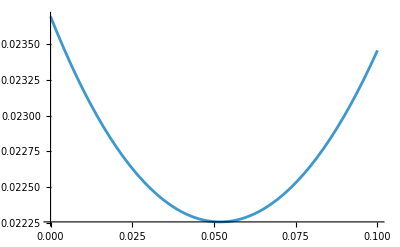

```mathematica
Plot[Det@gS[0,1,2,{R,1.}],{R,0,0.1},PlotRange->All]
```

Check that all derivatives of metric continue:

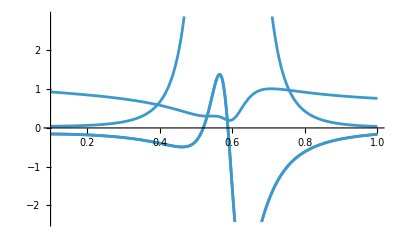

```mathematica
Plot[gS[0,1,2,{R,2.}],{R,0.1,1}]
```

```mathematica
optDens={PlotLegends->BarLegend[Automatic,LegendLabel->"g"],PlotPoints->10,PlotRangePadding->None,ColorFunction->"BlueGreenYellow",PlotRange->{-1.5,1.5},ColorFunctionScaling->False,Exclusions->None,FrameLabel->{"X","Y"}};
```

```mathematica
fontL={Frame->True,Axes->False,ImageSize->Medium,BaseStyle->{Black,FontFamily->"Times New Roman",FontSize->18},AxesStyle->Directive[FontSize->18],TicksStyle->Directive[FontSize->18],LabelStyle->{Black,FontFamily->"Times New Roman",FontSize-> 18}};
```

```mathematica
plotg[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ]:=
Show[DensityPlot[ArcTan[gS[hNum,levelOut,levelIn,{SCToSR[X,Y][[1]],SCToSR[X,Y][[2]]}][[#[[1]],#[[2]]]]],{X,-0.6,0.6},{Y,-0.6,0.6},Evaluate@fontL,Evaluate@optDens],plotDPs[hNum]]&/@{{1,1},{1,2},{2,2}}
```

```mathematica
G1S[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,{λ_?NumericQ,χ_?NumericQ},wp_:10]:=Module[{dg,gInv},
dg={ND[gS[hNum,levelOut,levelIn,{l,χ}],l,λ,Terms->7,Scale->0.001,WorkingPrecision->wp],
ND[gS[hNum,levelOut,levelIn,{λ,c}],c,χ,Terms->7,Scale->0.001,WorkingPrecision->wp]};

gInv=1/2 Inverse[gS[hNum,levelOut,levelIn,{λ,χ}]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2S[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,{λ_?NumericQ,χ_?NumericQ},wp_:10]:=Module[{dg,gInv},
dg={ND[gS[hNum,levelOut,levelIn,{l,χ}],l,λ,Terms->7,Scale->0.001,WorkingPrecision->wp],
ND[gS[hNum,levelOut,levelIn,{λ,c}],c,χ,Terms->7,Scale->0.001,WorkingPrecision->wp]};
gInv=1/2 Inverse[gS[hNum,levelOut,levelIn,{λ,χ}]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
optGamma={PlotLegends->BarLegend[Automatic,LegendLabel->"Γ"],PlotPoints->10,Exclusions->None,PlotRangePadding->None,ColorFunction->"BlueGreenYellow",FrameLabel->{"x","y"},ImageSize->250};
PlotGamma[G_,hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,wp_:10]:=Module[{memoG},
Internal`WithLocalSettings[Null,
memoG[x_,y_]:=memoG[x,y]=With[{sc=SCToSR[x,y]},ArcTan@G[hNum,levelOut,levelIn,{sc[[1]],sc[[2]]},wp]];
ParallelTable[DensityPlot[memoG[X,Y][[i]],{X,-0.6,0.6},{Y,-0.6,0.6},Evaluate@optGamma],{i,Range[3]}],
Clear[memoG] ]
]
```

## Plots

```mathematica
{zMin,zMax}={-Pi/2,Pi/2};
colorMapping=(Blend[{Cyan,White,Black},Rescale[#,{zMin,zMax}]]&);
piTicksLegend={{zMin,"-π/2"},{0,"0"},{zMax,"\\pi/2"}};

optDensShared={PlotPoints->30,Exclusions->None,FrameLabel->{"R cos Φ","R sin Φ"},ColorFunctionScaling->False,ColorFunction->colorMapping};

customBarRight=Labeled[DensityPlot[x,{x,zMin,zMax},{y,0,1},ColorFunctionScaling->False,ColorFunction->colorMapping,AspectRatio->1/13,FrameTicks->{{None,None},{piTicksLegend,None}},ImageSize->140],"atan g_μν",Left];
metricLabels=<|{1,1}->"g_RR",{1,2}->"g_RΦ",{2,2}->"g_ΦΦ"|>;

plotg[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ]:=Table[Show[DensityPlot[ArcTan[gS[hNum,levelOut,levelIn,{SCToSR[X,Y][[1]],SCToSR[X,Y][[2]]}][[idx[[1]],idx[[2]]]]],{X,-0.7,0.7},{Y,-0.7,0.7},Evaluate@optDensShared,PlotRange->{Automatic,Automatic,{zMin,zMax}},
Epilog->{Inset[metricLabels[idx],Scaled[{0.11,0.94}]]}
],plotDPs[hNum]],{idx,{{1,1},{1,2},{2,2}}}];
```

```mathematica
metricElements=Legended[Quiet@ResourceFunction["PlotGrid"][Transpose@{plotg[0,1,2]}],Placed[customBarRight,Top]]
```

-Graphics-

## Plotting functions for geodesics

```mathematica
plotRangeSR={{-0.7,0.7},{-0.7,0.7}};
```

```mathematica
markersize=0.1;
linethickness=0.015;
plotDP0Geod=Show[ParametricPlot[1/2{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{MyBlue,Dashed,Thickness[linethickness]}],ListPlot[{{0,DP1Out}},PlotStyle->MyRed,PlotMarkers->{vMarker,markersize}],ListPlot[{{0,-DP1In}},PlotStyle->MyRed,PlotMarkers->{uMarker,markersize}]];
plotDP1Geod=Show[ParametricPlot[1/2{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->{MyRed,Dashed,Thickness[linethickness]}],ListPlot[{{0,-DP1Out}},PlotStyle->MyBlue,PlotMarkers->{uMarker,markersize}],
ListPlot[{{0,DP1In}},PlotStyle->MyBlue,PlotMarkers->{vMarker,markersize}]];
```

```mathematica
{zMin,zMax}={0,π/2};
colorMapping=(Blend[{Black,White},Rescale[#,{zMax,zMin}]^(1/3)]&);

optDensEndif={PlotPoints->30,Exclusions->None,PlotRange->{0,π/2},ColorFunction->colorMapping,ColorFunctionScaling->False,FrameLabel->{"R cos Φ","R sin Φ"}};
```

```mathematica
PlotDPFixed[Hindex_,n1_?IntegerQ,n2_?IntegerQ]:=DensityPlot[ArcTan@Det@gS[Hindex,n1,n2,{SCToSR[X,Y][[1]],SCToSR[X,Y][[2]]}],{X,plotRangeSR[[1,1]],plotRangeSR[[1,2]]},{Y,plotRangeSR[[2,1]],plotRangeSR[[2,2]]},Evaluate@optDensEndif,PlotRange->{0,Pi/2}]

ppps={Show[PlotDPFixed[0,2,1],plotDP0Geod],Show[PlotDPFixed[1,1,2],plotDP1Geod]};
```

```mathematica
plotbg[hNum_]:=ppps[[hNum+1]]
```

```mathematica
getTimesFromSolve[list_]:=Table[list[[i,1,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
```

```mathematica
PlotSols[solMulti_List,tmax_,style_:"None"]:=Module[{numPaths,maxTimes},numPaths=Length[solMulti];
maxTimes=ConstantArray[tmax,Length[solMulti]];
Table[ParametricPlot[
Evaluate[SRToSC[{λ[t],χ[t]}]/. solMulti[[i]]],{t,0,maxTimes[[i]]},
PlotRange->All,Frame->True,PlotStyle->{geodColor,Thickness[geodThickness],ToExpression@style},AspectRatio->1,ColorFunctionScaling->False]
,{i,1,numPaths}]
]
```

```mathematica
(*energy function E(t)=g_{11} R'^2+2 g_{12} R' Φ'+g_{22} Φ'^2*)
PlotEnergyTest[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,sol_,tmax_:tmax]:=Quiet@Module[{energy},
energy[t_]:=Evaluate[With[{
rr=First[λ[t]/. sol],
pp=First[χ[t]/. sol],
rpd=First[λ'[t]/. sol],
ppd=First[χ'[t]/. sol]},
rpd^2 gS[hNum,levelOut,levelIn,{rr,pp}][[1,1]]+2 rpd ppd gS[hNum,levelOut,levelIn,{rr,pp}][[1,2]]+ppd^2 gS[hNum,levelOut,levelIn,{rr,pp}][[2,2]]]
];

Plot[Abs@energy[t],{t,0,tmax},Frame->True,PlotRange->All,FrameLabel->{"t","E(t)"},PlotLabel->"Conserved Energy along the Geodesic",ScalingFunctions->"Log",ImageSize->300]
]
```

```mathematica
PlotGeod[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,sol_,tmax_:tmax]:={PlotEnergyTest[hNum,levelOut,levelIn,sol,tmax],Show[plotbg[hNum],PlotSols[sol,tmax],
PlotRange->plotRangeSR,
ImageSize->220]}
```

```mathematica
shift={{0,-Bz2},{0,Bz2},{0,0}};
```

```mathematica
PlotSolsCart[hNum_,solMulti_List,tmax_,sensitivity_:1.0]:=Module[{numPaths,maxTimes},numPaths=Length[solMulti];
maxTimes=ConstantArray[tmax,numPaths];
Table[ParametricPlot[Evaluate[shift[[hNum+1]]+RToC@SRToR[{λ[t],χ[t]}]/. solMulti[[i]]],{t,0,maxTimes[[i]]},PlotRange->All,Frame->True,PlotStyle->{Thickness[geodThickness/2]},AspectRatio->1,ColorFunction->geodColor],{i,1,numPaths}]]

PlotGeodCart[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,sol_,sensitivity_:1.0,tmax_:tmax]:=Show[
bgM1Cart[[levelOut]],
PlotSolsCart[hNum,sol,tmax,sensitivity],PlotRange->{{-0.33,0.33},{-0.33,0.33}},ImageSize->Medium
]
```

## Geodesics

```mathematica
(*λ,χ represent shifted radial coordinates, as these are the main ones in which metric works. hNum chooses which one (with respect to which DP) the coordinate is taken*)
```

```mathematica
Clear[eq,sol,tmax,cauchy]
```

```mathematica
tmax=5;
eq[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,wp_:10]:={
λ''[t]+G1S[hNum,levelOut,levelIn,{λ[t],χ[t]},wp].{λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2S[hNum,levelOut,levelIn,{λ[t],χ[t]},wp].{λ'[t]^2,2λ'[t]χ'[t], χ'[t]^2}==0
};

cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
stopEvent={WhenEvent[λ[t]<10^-3,"StopIntegration"]};
sol[hNum_?IntegerQ,levelOut_?IntegerQ,levelIn_?IntegerQ,{λ0_,χ0_},{λd0_,χd0_},tmax_:10,prec_:10,wp_:30]:=NDSolve[Join[eq[hNum,levelOut,levelIn,wp],cauchy[λ0,χ0,λd0,χd0],stopEvent],{λ,χ},{t,0,tmax}
,Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->7}}
,PrecisionGoal->prec,AccuracyGoal->prec,WorkingPrecision->wp
]
```

### Transforming velocity

```mathematica
getInitCondition[sol_,t_?NumericQ]:=<|"Position"->First[{λ[t],χ[t]}/. sol],"Velocity"->First[{λ'[t],χ'[t]}/. sol]|>
```

```mathematica
(*keep angle continuous near a reference*)
NormalizeAngle[θ_,θref_]:=θ+2 π Round[(θref-θ)/(2 π)];

(*SR->global Cartesian,given the center shift V*)
SRToCartWithShift[{R_,Φ_},V_]:=V+RToC@SRToR[{R,Φ}];

(*master transform from SR0 (center A) to SR1 (center B)*)
Clear[TransformState]
Options[TransformState]={"Branch"->"Out"};  (*"Out" or "In"*)
TransformState[CAToCB_,posS0:{R0_?NumericQ,Φ0_?NumericQ},velS0:{Ṙ0_?NumericQ,Φ̇0_?NumericQ},OptionsPattern[]]:=Module[{branch=OptionValue["Branch"],F,pos1,J,φref,posCart},
(*composite mapping SR0->(shifted) Cart->SR1,with chosen branch*)
F[R_,Φ_]:=With[{xy=CAToCB@RToC@SRToR[{R,Φ}]},If[branch==="Out",RToSROut@CToR[xy],RToSRIn@CToR[xy]]];
(*position in SR1*)
pos1=F[R0,Φ0];
(*unwrap angle to be continuous w.r.t.the physical polar angle of xy*)
posCart=CAToCB@RToC@SRToR[{R0,Φ0}];
φref=CToR[posCart][[2]];
pos1={pos1[[1]],NormalizeAngle[pos1[[2]],If[branch==="Out",φref,φref-π]]};
(*push forward the velocity via total Jacobian*)
J=D[F[R,Φ],{{R,Φ}}]/. {R->R0,Φ->Φ0};
{pos1,J.velS0}];

(*convenience wrappers for your DPs*)
TransformDP0toDP1[posS0_,velS0_,branch_:"Out"]:=TransformState[C0ToC1,posS0,velS0,"Branch"->branch];
TransformDP0toDP2[posS0_,velS0_,branch_:"Out"]:=TransformState[C0ToC2,posS0,velS0,"Branch"->branch];
TransformDP1toDP2[posS0_,velS0_,branch_:"Out"]:=TransformState[C1ToC2,posS0,velS0,"Branch"->branch];
```

```mathematica
(*CAToCB:Centering function,e.g.,C0ToC1*)(*posCart:{Bx,Bz} global coordinates*)(*velCart:{vBx,vBz} global velocity*)CartToSRState[CAToCB_,posCart_List,velCart_List,OptionsPattern[{"Branch"->"Out"}]]:=Module[{branch=OptionValue["Branch"],relPos,R0,Φ0,J,mapping,x,y,φref},(*Shift global coordinates to local Cartesian frame relative to DP*)relPos=CAToCB[posCart];
(*Map position to SR space using your exact logic*)
{R0,Φ0}=If[branch==="Out",RToSROut[CToR[relPos]],RToSRIn[CToR[relPos]]];
(*Continuity unwrapping for the angle*)
φref=CToR[relPos][[2]];
Φ0=NormalizeAngle[Φ0,If[branch==="Out",φref,φref-π]];
(*Define the mapping F:(x,y)->(R,ϕ) for Jacobian*)
mapping[xx_,yy_]:=With[{pol={Sqrt[xx^2+yy^2],ArcTan[xx,yy]}},If[branch==="Out",RToSROut[pol],RToSRIn[pol]]];
(*Calculate Jacobian matrix at the localized point*)
J=D[mapping[x,y],{{x,y}}]/. {x->relPos[[1]],y->relPos[[2]]};
(*Return values in your sol format*)
{{R0,Φ0},J.velCart}]
```

```mathematica
CartToSRState[CAToCB_,posCart_List,velCart_List,OptionsPattern[{"Branch"->"Out"}]]:=Module[{branch=OptionValue["Branch"],relPos,r,φ,R0,Φ0,factor,J,x,y},(*1. Shift to DP-centered frame*)relPos=CAToCB[posCart];
{x,y}=relPos;
r=Sqrt[x^2+y^2];
φ=ArcTan[x,y];
(*Position in SR coordinates*)
If[branch==="Out",R0=(r+Sqrt[1+r^2])/2;
Φ0=Mod[φ,2 π];
factor=(1/r+1/Sqrt[1+r^2])/2,(*In branch*)R0=(-r+Sqrt[1+r^2])/2;
Φ0=Mod[φ-π,2 π];
factor=(-1/r+1/Sqrt[1+r^2])/2];
(*Analytic Jacobian:J=∂(R,Φ)/∂(x,y)*)J={{x*factor,y*factor},(*∂R/∂x,∂R/∂y*){-y/r^2,x/r^2}            (*∂Φ/∂x,∂Φ/∂y*)};
(*Angle continuity*)Φ0=NormalizeAngle[Φ0,If[branch==="Out",φ,φ-π]];
{{R0,Φ0},J.velCart}]
```

### Plotting functions for Cartesian

```mathematica
DH1C[x_,y_]=D[H[x,y],x]//Simplify
DH2C[x_,y_]=D[H[x,y],y]//Simplify
```

{{0,14 √2,0},{14 √2,0,14 √2},{0,14 √2,0}}

{{28,0,0},{0,0,0},{0,0,-28}}

```mathematica
gC[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{dim,dh1c,dh2c,enNonSort,eigNonSort,en,eig,M1,M1T,M2,M2T,endif,g11,g12,g22,levels},
(*labeled as n=1,2,3 states*)
dim=3;
levels=DeleteCases[Range[3],n];
{enNonSort,eigNonSort}=Eigensystem[H[λ,χ]];
eigNonSort=Map[Normalize,eigNonSort];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
dh1c=DH1C[λ,χ];
dh2c=DH2C[λ,χ];

M1=Conjugate[eig⟦n⟧].dh1c.eig⟦#⟧&/@levels;
M1T=Conjugate[eig⟦#⟧].dh1c.eig⟦n⟧&/@levels;
M2=Conjugate[eig⟦n⟧].dh2c.eig⟦#⟧&/@levels;
M2T=Conjugate[eig⟦#⟧].dh2c.eig⟦n⟧&/@levels;
endif=(en⟦n⟧-en⟦#⟧)^2&/@levels;

g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
markersize=0.1;
bgDP0Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{uMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{uMarker,markersize}]]
bgDP1Cart:=Show[ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{vMarker,markersize}],ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{vMarker,markersize}]]
bgDP2Cart:=Show[ListPlot[{{0,0}},PlotStyle->MyGreen,PlotMarkers->{plus,markersize}]]
```

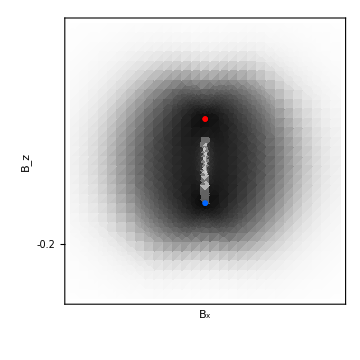
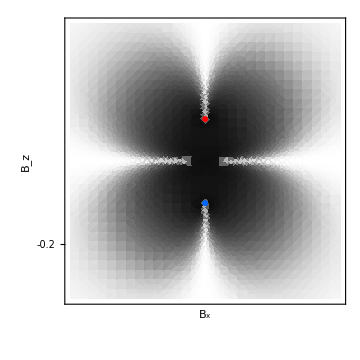
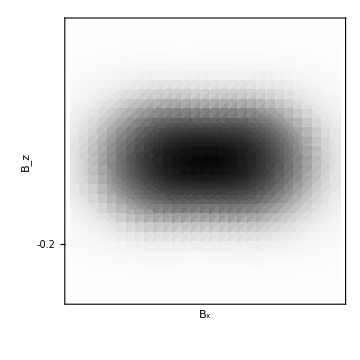

```mathematica
bgM1Cart=Table[With[{dynamicLegend=DensityPlot[x,{y,0,1},{x,zMin,zMax},
ColorFunctionScaling->False,ColorFunction->colorMapping,AspectRatio->12,PlotRangePadding->None,Frame->True,
FrameTicks->{{None,piTicks},{None,None}},ImageSize->34]},
Legended[Show[{DensityPlot[Quiet@ArcTan@Det@gC[ii,x,y],{x,-0.33,0.33},{y,-0.33,0.33},PlotLegends->False,
PlotPoints->30,
FrameLabel->{"B_x","B_z"},PlotRange->{0,π/2},PlotRangePadding->None,ClippingStyle->Yellow,
FrameTicks->Chop@{{Range[-5,5,0.1],None},{Range[-5,5,0.1],None}},ColorFunctionScaling->False,ColorFunction->colorMapping,ImageSize->Medium],
{bgDP0Cart,bgDP1Cart,Graphics[]}[[ii]]}],
Placed[dynamicLegend,Right]]],{ii,1,3}]
```

```mathematica
(*Distances along geodesic*)
ds[hNum_,levelOut_,levelIn_,sol_,t_]:=Module[{der,g},
der=First[{λ'[t],χ'[t]}/.sol];
g=First[gS[hNum,levelOut,levelIn,{λ[t],χ[t]}]/.sol];
√(der.g.der)
]
Dist[hNum_,levelOut_,levelIn_,sol_,tMin_,tMax_]:=NIntegrate[ds[hNum,levelOut,levelIn,sol,t],{t,tMin,tMax}]

dsCart[n_,sol_,t_]:=Module[{der,g},
der=First[{λ'[t],χ'[t]}/.sol];
g=First[gC[n,λ[t],χ[t]]/.sol];
√(der.g.der)
]
DistCart[n_,sol_,tMin_,tMax_]:=NIntegrate[dsCart[n,sol,t],{t,tMin,tMax}]
```

## Plots

### Crossing impassable line: 1.s. ->DP0 g.s. ->DP1 1.s. (we go to g.s. because on 1.s. there is impassable line, horizontal from DP2 in middle)

#### Original passage in SR

```mathematica
θin=0.4675;
initPosInOriginal={-0.1,-0.2};
initVel={Cos[θin],Sin[θin]};
{statePos,stateVel}=CartToSRState[C2ToC0,initPosInOriginal,initVel,"Branch"->"Out"]
```

{{0.575311,-2.36088},{-0.541978,2.1889}}

Test for the transformation, should give (0, 0 mod 2π):

```mathematica
RToSROut@CToR@C2ToC0@initPosInOriginal-statePos
```

```mathematica
sol1=Quiet@sol[0,2,1,statePos,stateVel,0.4,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

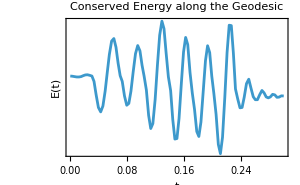
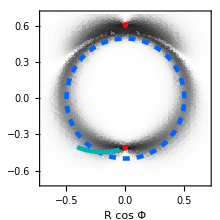

```mathematica
timeSwitch1=0.3; (*check that the energy is approximately constant, switch before it breaks*)
plotgeod1=PlotGeod[0,2,1,sol1,timeSwitch1]
```

```mathematica
cut1=getInitCondition[sol1,timeSwitch1]
{Position1,Velocity1}=TransformDP0toDP1[cut1["Position"],cut1["Velocity"],"Out"]
```

<|Position→{0.428582,-1.68731},Velocity→{-0.3986,2.27341}|>

{{0.526373,-1.21345},{-0.524597,2.26404}}

```mathematica
sol2=Quiet@sol[1,1,2,Position1,Velocity1,0.2,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

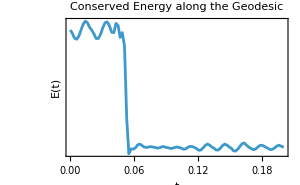
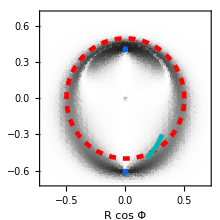

```mathematica
timeSwitch2=0.2; (*here is some small numerical bump, but still within precision limit*)
plotgeod2=PlotGeod[1,1,2,sol2,timeSwitch2]
```

#### Distance along geodesic

```mathematica
timeSwitch2Cut=timeSwitch2;
```

```mathematica
p1[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol1]
p2[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol2]
```

```mathematica
tDP0=Quiet@FindRoot[p1[t][[#]],{t,0.1}]&/@{1,2}
tDP1=Quiet@FindRoot[p2[t][[#]],{t,0.04}]&/@{1,2}
```

{{t→0.142656},{t→0.142656}}

{{t→0.0512975},{t→0.0512975}}

```mathematica
dist1=Dist[0,2,1,sol1,0,timeSwitch1]
part1=Plot[Dist[0,2,1,sol1,0,tt],{tt,0,timeSwitch1}];
```

0.644989

```mathematica
dist2=Dist[1,1,2,sol2,0,timeSwitch2Cut]
part2=Plot[dist1+Dist[1,1,2,sol2,0,tt-timeSwitch1],{tt,timeSwitch1,timeSwitch1+timeSwitch2Cut},PlotStyle->Red];
```

0.429992

```mathematica
(*Distance to DPs*)
DPTimes={t/.tDP0[[1]],t/.tDP1[[1]]}
distToDP1=Dist[0,1,2,sol2,0,DPTimes[[2]]]
dist1+distToDP1
```

{0.142656,0.0512975}

0.0716458

0.716634

Distance along geodesic should be linear, this is another test for geodesic.

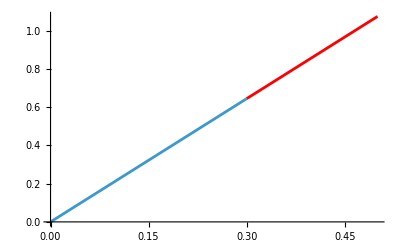

```mathematica
Show[{part1,part2},PlotRange->All]
```

The linear increase is necessary, as the geodesical speed is constant.

to the final point after passing through DP0 and DP1 back to M^0: (x_f, y_f)=
(check in the plot combinedGeod)

```mathematica
shift[[3]]+RToC@SRToR@First[{λ[timeSwitch2Cut],χ[timeSwitch2Cut]}/.sol2]
```

{-0.105428,0.101714}

The total geometric distance of such a path is s=

```mathematica
dist1+dist2
```

1.07498

#### Perturbation (plus)

```mathematica
θinP=θin+0.1;
initPosInOriginal={-0.1,-0.2};
initVel={Cos[θinP],Sin[θinP]};
{statePos,stateVel}=CartToSRState[C2ToC0,initPosInOriginal,initVel,"Branch"->"Out"]
```

{{0.575311,-2.36088},{-0.556794,1.50324}}

```mathematica
sol1p=Quiet@sol[0,2,1,statePos,stateVel,1,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

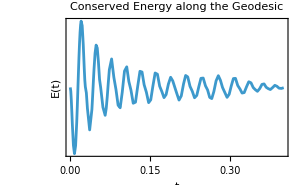
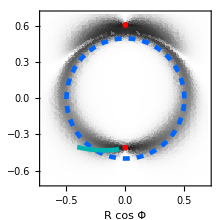

```mathematica
timeSwitch1p=0.4;
plotgeod1p=PlotGeod[0,2,1,sol1p,timeSwitch1p]
```

```mathematica
cut1p=getInitCondition[sol1p,timeSwitch1p]
{Position1,Velocity1}=TransformDP0toDP1[cut1p["Position"],cut1p["Velocity"],"Out"]
```

<|Position→{0.424657,-1.70146},Velocity→{-0.231731,1.74765}|>

{{0.522828,-1.0717},{-0.321616,2.10427}}

```mathematica
sol2p=Quiet@sol[1,1,2,Position1,Velocity1,0.6,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

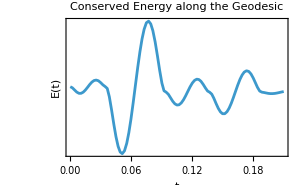
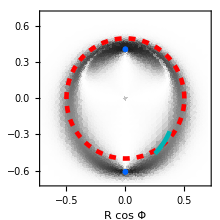

```mathematica
timeSwitch2p=0.2101;
plotgeod2p=PlotGeod[1,1,2,sol2p,timeSwitch2p]
```

#### Distance along geodesic

The final time is set so the geodesic travels the same distance as unperturbed one.

```mathematica
timeSwitch2Cut=0.2101;
```

```mathematica
p1[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol1p]
p2[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol2p]
```

```mathematica
tDP0=Quiet@FindRoot[p1[t][[#]],{t,0.1}]&/@{1,2}
tDP1=Quiet@FindRoot[p2[t][[#]],{t,0.04}]&/@{1,2}
```

{{t→0.159594},{t→0.159594}}

{{t→0.0745894},{t→0.0745894}}

```mathematica
DPTimes={t/.tDP0[[1]],t/.tDP1[[1]]}
```

{0.159594,0.0745894}

```mathematica
dist1=Dist[0,2,1,sol1p,0,timeSwitch1p]
part1=Plot[Dist[0,2,1,sol1p,0,tt],{tt,0,timeSwitch1p}];
```

0.701368

```mathematica
dist2=Dist[1,1,2,sol2p,0,timeSwitch2Cut]
part2=Plot[dist1+Dist[1,1,2,sol2p,0,tt-timeSwitch1p],{tt,timeSwitch1p,timeSwitch1p+timeSwitch2Cut},PlotStyle->Red];
```

0.368394

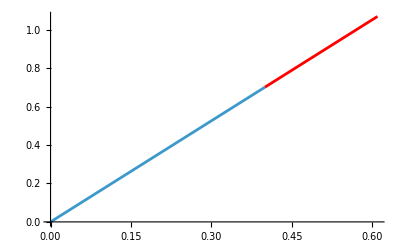

```mathematica
Show[{part1,part2},PlotRange->All]
```

```mathematica
shift[[3]]+RToC@SRToR@First[{λ[timeSwitch2Cut],χ[timeSwitch2Cut]}/.sol2]
```

{-0.114642,0.105824}

```mathematica
dist1+dist2
```

1.06976

#### Perturbation (minus)

```mathematica
θinM=θin-0.1;
initPosInOriginal={-0.1,-0.2};
initVel={Cos[θinM],Sin[θinM]};
{statePos,stateVel}=CartToSRState[C2ToC0,initPosInOriginal,initVel,"Branch"->"Out"]
```

{{0.575311,-2.36088},{-0.521746,2.85269}}

```mathematica
sol1m=Quiet@sol[0,2,1,statePos,stateVel,1,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

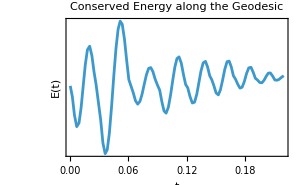
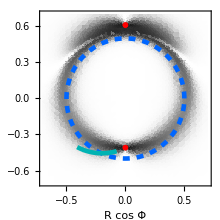

```mathematica
timeSwitch1m=0.22;
plotgeod1m=PlotGeod[0,2,1,sol1m,timeSwitch1m]
```

```mathematica
cut1m=getInitCondition[sol1m,timeSwitch1m]
{Position1,Velocity1}=TransformDP0toDP1[cut1m["Position"],cut1m["Velocity"],"Out"]
```

<|Position→{0.444899,-1.73871},Velocity→{-0.605313,2.80143}|>

{{0.546297,-1.34839},{-0.75723,2.45885}}

```mathematica
sol2m=Quiet@sol[1,1,2,Position1,Velocity1,0.8,10,10]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

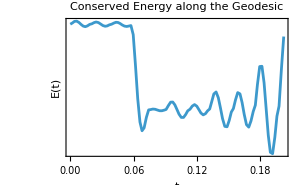
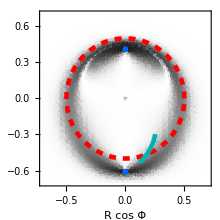

```mathematica
timeSwitch2m=0.202;
plotgeod2m=PlotGeod[1,1,2,sol2m,timeSwitch2m]
```

#### Distance along geodesic

```mathematica
timeSwitch2Cut=0.20;
```

```mathematica
p1[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol1m]
p2[t_]:=First[RToC@SRToR@{λ[t],χ[t]}/.sol2m]
```

```mathematica
tDP0=Quiet@FindRoot[p1[t][[#]],{t,0.1}]&/@{1,2}
tDP1=Quiet@FindRoot[p2[t][[#]],{t,0.04}]&/@{1,2}
```

{{t→0.130055},{t→0.130055}}

{{t→0.0601342},{t→0.0601342}}

```mathematica
DPTimes={t/.tDP0[[1]],t/.tDP1[[1]]}
```

{0.130055,0.0601342}

```mathematica
dist1=Dist[0,2,1,sol1m,0,timeSwitch1m]
part1=Plot[Dist[0,2,1,sol1m,0,tt],{tt,0,timeSwitch1m}];
```

0.558065

```mathematica
dist2=Dist[1,1,2,sol2m,0,timeSwitch2Cut]
part2=Plot[dist1+Dist[1,1,2,sol2m,0,tt-timeSwitch1m],{tt,timeSwitch1m,timeSwitch1m+timeSwitch2Cut},PlotStyle->Red];
```

0.512405

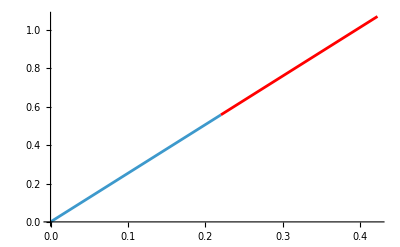

```mathematica
Show[{part1,part2},PlotRange->All]
```

```mathematica
shift[[3]]+RToC@SRToR@First[{λ[timeSwitch2Cut],χ[timeSwitch2Cut]}/.sol2]
```

{-0.105428,0.101714}

```mathematica
dist1+dist2
```

1.07047

#### Putting together

```mathematica
plotgeod12=Quiet@ResourceFunction["PlotGrid"][{{plotgeod1[[2]]},{plotgeod2[[2]]}}];
```

```mathematica
combinedM0=Show[plotgeod1[[2]],PlotSols[sol1p,timeSwitch1p,"Opacity[0.5]"],PlotSols[sol1m,timeSwitch1m,"Opacity[0.5]"],PlotRange->plotRangeSR ];
combinedM1=Show[plotgeod2[[2]],PlotSols[sol2p,timeSwitch2p,"Opacity[0.5]"],PlotSols[sol2m,timeSwitch2m,"Opacity[0.5]"],PlotRange->plotRangeSR];
plotgeod12=Quiet@ResourceFunction["PlotGrid"][{{combinedM0},{combinedM1}}]
```

-Graphics-

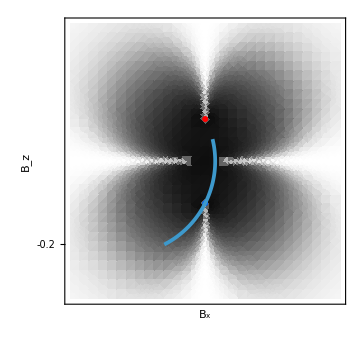

```mathematica
ppa=PlotGeodCart[0,2,1,sol1,1,timeSwitch1]
```

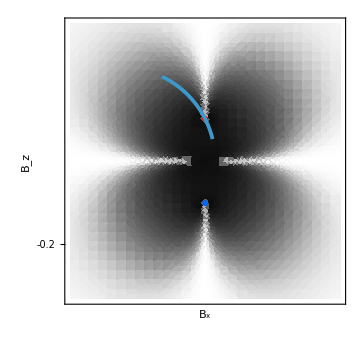

```mathematica
ppb=PlotGeodCart[1,2,1,sol2,1,0.2]
```

## Geodesics balls in Cartesian (beware: rewriting previous functions), and combined geodesics plot over cartesian sace

```mathematica
G1Cart[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gC[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gC[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gC[n,λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2Cart[n_?IntegerQ,λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,scale,c,l,dg,gInv},
derTerms=8;
scale=0.001;
dg={ND[gC[n,l,χ],l,λ,Terms->derTerms,Scale->scale],ND[gC[n,λ,c],c,χ,Terms->derTerms,Scale->scale]};
gInv=1/2 Inverse[gC[n,λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],
Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
tmax=10;
eqCart[n_?IntegerQ]:={
λ''[t]+G1Cart[n,λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2Cart[n,λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

```mathematica
singStopCart=0.003;
stopEventCart={WhenEvent[(*√(λ[t]^2+χ[t]^2)<singStop||*)√(λ[t]^2+(χ[t]+Bz2)^2)<singStopCart||√(λ[t]^2+(χ[t]-Bz2)^2)<singStopCart,"StopIntegration"]};
cauchyCart[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solCart[n_,λ0_,χ0_,λd0_,χd0_,tmax_:10,prec_:10,workingprecision_:30]:=Quiet@NDSolve[Join[eqCart[n],cauchyCart[λ0,χ0,λd0,χd0],stopEventCart],{λ,χ},{t,0,tmax}
,Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}}
,PrecisionGoal->prec,AccuracyGoal->prec,WorkingPrecision->workingprecision]
solCart::usage="sol[n,λ0_,χ0_,λd0_,χd0_,tmax_:10,prec_:10,workingprecision_:30] 
Calculates the geodesic for: 
n=state manifold level {1,2,3},
{λ0,χ0}=initial values, 
{λd0,χd0}=initial velocities, 
tmax=max. time of evolution, 
prec=WorkingGoal,AccuracyGoal of NDSolve,
workingprecision=WorkingPrecision of NDSolve.";
```

```mathematica
PlotSolsCombined[solMulti_List,sensitivity_:1.0,zShift_:0.0]:=Module[{numPaths,maxTimes,colorFunc},numPaths=Length[solMulti];
maxTimes=getTimesFromSolve[solMulti];
Table[ParametricPlot[{λ[t],χ[t]+zShift}/. solMulti[[i]],{t,0,maxTimes[[i]]},PlotRange->All,Frame->True,FrameLabel->{"λ","χ"},PlotStyle->Thickness[0.005],AspectRatio->1,PlotPoints->100,ColorFunction->geodColor],{i,1,numPaths}]];

singlePlot[solMulti_List,sensitivity_:1.0,zShift_:0.0]:=Show[PlotSolsCombined[solMulti,sensitivity,zShift],PlotRange->{{-3.4,3.4},{-3.4,3.4}},ImageSize->500]
```

```mathematica
markersize=13;
bgCartDP1=ListPlot[{{{0,-Bz2}},{{0,Bz2}}},PlotStyle->{Directive@MyBlue,Directive@MyRed},PlotMarkers->{uMarker,markersize}];
bgCartDP2=ListPlot[{{{0,-Bz2}},{{0,Bz2}}},PlotStyle->{Directive@MyBlue,Directive@MyRed},PlotMarkers->{{vMarker,markersize},{vMarker,markersize}}];
bgCartDP3=Graphics[];
```

### Plotting

```mathematica
{zMin,zMax}={0,π/2};
bds={-0.34,0.34};
colorMapping=(Blend[{Black,White},Rescale[#,{zMax,zMin}]^(1/3)]&);
```

```mathematica
commonOpts={PlotRangePadding->None,PlotRange->{zMin,zMax},ColorFunction->colorMapping,ColorFunctionScaling->False};
```

### Geodesic ball Plots

Initial coordinate on M1 above was chosen as {0.6`10, -2`10}, {-1.`10, 0.3`10}

```mathematica
{xin,yin}={-0.1,-0.2}
Ngeodesics=60;
```

{-0.1,-0.2}

So we plot the geodesic ball on ground state and first excited state manifold (1.s. corresponds to what we have above, g.s. shows impassable lines)

```mathematica
(*First state*)
```

```mathematica
solMulti1=Flatten[ParallelTable[solCart[1,xin,yin,Cos[p],Sin[p],10,10,50],{p,0,2π,2π/Ngeodesics}],1];
```

```mathematica
plotGeodball1=Show[singlePlot[solMulti1,1.0,0],bgCartDP1];
```

```mathematica
solMulti2=Flatten[ParallelTable[solCart[2,xin,yin,Cos[p],Sin[p],10,10,50],{p,0,2π,2π/Ngeodesics}],1];
```

```mathematica
plotGeodball2=Show[singlePlot[solMulti2,1.0,0],bgCartDP2];
```

```mathematica
solMulti3=Flatten[ParallelTable[solCart[3,xin,yin,Cos[p],Sin[p],20,8,30],{p,0,2π,2π/Ngeodesics}],1];
```

```mathematica
plotGeodball3=Show[singlePlot[solMulti3,1.0,0]];
```

```mathematica
plotBall[i_]:={plotGeodball1,plotGeodball2,plotGeodball3}[[i]]
```

```mathematica
clippedGeodInset[level_,{xmin_,xmax_},{ymin_,ymax_}]:=Inset[Show[plotBall[level],PlotRange->{{xmin,xmax},{ymin,ymax}},Frame->None,Axes->None,Background->None],{xmin,ymin},{Left,Bottom},{xmax-xmin,ymax-ymin}];
```

```mathematica
mainPlots=Table[Module[{baseDensity,overlays},
baseDensity=ListDensityPlot[bgData[[level]],DataRange->{bds,bds},Evaluate@listCommonOpts];
overlays={clippedGeodInset[level,bds,bds],If[level==1,{Red,Dashed,Line[{{0,-Bz2},{0,Bz2}}]},{}],If[level==2,{Red,Dashed,InfiniteLine[{0,0},{1,0}],Line[{{0,-0.34},{0,-Bz2}}],Line[{{0,Bz2},{0,0.34}}]},{}]};
Show[baseDensity,Epilog->overlays,PlotRange->{bds,bds},AspectRatio->1]],{level,1,3}];

Quiet@ResourceFunction["PlotGrid"][{mainPlots},PlotRange->All,ImageSize->510,Spacings->0]
```

-Graphics-

### Unstable geodesic crossing the impassable line

```mathematica
PlotEnergyTestCart[n_,sol_,tmax_:tmax]:=Quiet@Module[{energy},
energy[t_]:=Evaluate[With[{
rr=First[λ[t]/. sol],
pp=First[χ[t]/. sol],
rpd=First[λ'[t]/. sol],
ppd=First[χ'[t]/. sol]},
rpd^2 gC[n,rr,pp][[1,1]]+2 rpd ppd gC[n,rr,pp][[1,2]]+ppd^2 gC[n,rr,pp][[2,2]]]
];

Plot[Abs@energy[t],{t,0,tmax},Frame->True,PlotRange->All,FrameLabel->{"t","E(t)"},PlotLabel->"Conserved Energy along the Geodesic",ScalingFunctions->"Log",ImageSize->300]
]
```

```mathematica
bg=ListDensityPlot[bgData[[2]],DataRange->{bds,bds},Evaluate@listCommonOpts];
```

```mathematica
timeBottom=0.4493303295856692;
solBottom=solCart[2,-0.43427592506437374,-10^-3,0,-1,timeBottom,5,5];
```

```mathematica
{λ[timeBottom],χ[timeBottom]}/.solBottom
```

{{-0.1,-0.2}}

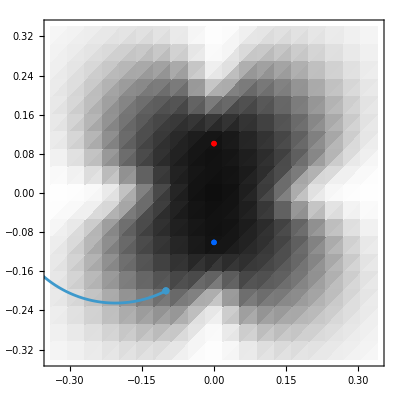

```mathematica
plotGeodBottom=Show[{bg,singlePlot[solBottom,1.,0],bgCartDP2,ListPlot[{{-0.1,-0.2}}]}]
```

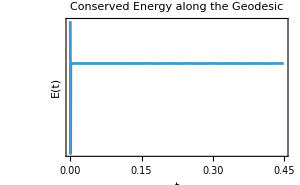

```mathematica
PlotEnergyTestCart[2,solBottom,timeBottom]
```

```mathematica
distBottom=DistCart[2,solBottom,0,timeBottom]
```

1.0375

```mathematica
timeUpper=timeBottom;
solUpper=solCart[2,-0.43427592506437374,10^-3,0,1,timeUpper,7,10];
```

```mathematica
{λ[timeUpper],χ[timeUpper]}/.solUpper
```

{{-0.1,0.2}}

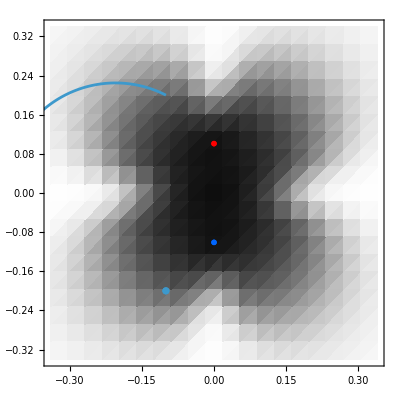

```mathematica
plotGeodBallUpper=Show[{bg,singlePlot[solUpper,1.0,0],bgCartDP2,ListPlot[{{-0.1,-0.2}}]}]
```

```mathematica
distUpper=DistCart[2,solUpper,0,timeUpper]
```

1.0375

```mathematica
distUpper+distBottom
```

2.075

#### Optimize for the final point and put back

I could have rewritten it to the boundary valued geodesics, but this optimization was faster (at least for human hours...definitely not for computer :) ):

```mathematica
objectiveDist[x0In_?NumericQ,tBottomIn_?NumericQ]:=Module[{solCross,val,target},
target={-0.1,-0.2};
solCross=solCart[2,x0In,-10^-3,0,-1,tBottomIn,6,6];
val={λ[tBottomIn],χ[tBottomIn]}/. solCross;
Norm[Flatten[val]-target]
];

optimalResult=Quiet@FindMinimum[objectiveDist[x0,tB],{{x0,-0.4},{tB,0.4}},AccuracyGoal->5,PrecisionGoal->5]
```

{0.00822757,{x0→-0.402524,tB→0.402325}}

#### Perturbed geodesics on bottom

Find the initial condition

```mathematica
fin={λ[timeBottom],χ[timeBottom]}/.solBottom[[1]]
finD=-{λ'[timeBottom],χ'[timeBottom]}/.solBottom[[1]]
```

{-0.1,-0.2}

{-0.958716,-0.483972}

```mathematica
ArcTan[finD[[2]]/finD[[1]]] (*angle of the initial geodesic to travel through DPs*)
```

0.46749

```mathematica
finDPlus=RotationMatrix[-0.01].finD
finDMinus=RotationMatrix[0.01].finD
```

{-0.963507,-0.474361}

{-0.953828,-0.493535}

```mathematica
timeBottomP=1;
solBottomP=solCart[2,fin[[1]],fin[[2]],finDPlus[[1]],finDPlus[[2]],timeBottomP,10,20];
timeBottomM=1;
solBottomM=solCart[2,fin[[1]],fin[[2]],finDMinus[[1]],finDMinus[[2]],timeBottomM,10,20];
```

### Putting all together with the shortcut

```mathematica
markersize=0.06;
plotpoints=50;

colorMapping=(Blend[{Black,White},Rescale[#,{zMax,zMin}]^(1/3)]&);
bgSplitCart=Show[
(*M2 background*)
DensityPlot[Quiet@ArcTan@Det@gC[2,x,y],{x,-0.47,0},{y,-0.33,0.33},PlotPoints->plotpoints,ColorFunction->colorMapping,ColorFunctionScaling->False,PlotRange->{0,Pi/2}],
(*M1 background*)
DensityPlot[Quiet@ArcTan@Det@gC[1,x,y],{x,0,0.04},{y,-0.33,0.33},Evaluate@fontL,PlotPoints->plotpoints,ColorFunction->colorMapping,ColorFunctionScaling->False,PlotRange->{0,Pi/2}],
(*DPs*)
ListPlot[{{0,-Bz2}},PlotStyle->MyBlue,PlotMarkers->{cross,markersize}],
ListPlot[{{0,Bz2}},PlotStyle->MyRed,PlotMarkers->{cross,markersize}],FrameLabel->{"B_x","B_z"},ImageSize->Medium];
```

```mathematica
PlotCombinedGeodCart[sol1_,sol2_,tmax1_,tmax2_,extraGeods_List:{}]:=Module[{finalPt1,finalPt2,path1,path2,extraPaths,densLegend,getPos,getPosCart,getDomainMax},(*Helper to prevent ParametricPlot from extrapolating past NDSolve's actual stopping time*)getDomainMax[s_,requestedTmax_]:=Min[requestedTmax,(λ["Domain"]/. s)[[1,2]]];
(*Coordinate mapping for the main SR geodesics*)
getPos[hIdx_,s_,t_]:=shift[[hIdx]]+RToC@SRToR[{λ[t],χ[t]}]/. s;
(*Coordinate mapping for the extra purely Cartesian geodesics*)
getPosCart[s_,t_]:={λ[t],χ[t]}/. s;
finalPt1=getPos[1,sol1[[1]],getDomainMax[sol1[[1]],tmax1]];
finalPt2=getPos[2,sol2[[1]],getDomainMax[sol2[[1]],tmax2]];
(*Default Paths (Mapped from SR)*)path1=Table[ParametricPlot[Evaluate@getPos[1,sol1[[i]],t],{t,0,getDomainMax[sol1[[i]],tmax1]},PlotStyle->Directive[geodColor,Thickness[0.006],CapForm["Round"]]],{i,Length@sol1}];
path2=Table[ParametricPlot[Evaluate@getPos[2,sol2[[i]],t],{t,0,getDomainMax[sol2[[i]],tmax2]},PlotStyle->Directive[geodColor,Thickness[0.006],CapForm["Round"]]],{i,Length@sol2}];
(*Universal Extra Geodesics Processing*)extraPaths=If[Length[extraGeods]>0,Flatten@Table[Module[{solObj,tmaxObj,styleObj,isCartesian,hIdx},solObj=extra[[1]];
styleObj=Last[extra];
(*Styles always at the end*)isCartesian=(Length[extra]==3);
If[isCartesian,(*Pure Cartesian case:{sol,tmax,{styles}}*)tmaxObj=extra[[2]];
ParametricPlot[Evaluate@getPosCart[solObj[[i]],t],{t,0,getDomainMax[solObj[[i]],tmaxObj]},PlotStyle->Directive@@Flatten[{Thickness[0.006],CapForm["Round"],styleObj}]],
hIdx=extra[[2]];
tmaxObj=extra[[3]];
ParametricPlot[Evaluate@getPos[hIdx,solObj[[i]],t],{t,0,getDomainMax[solObj[[i]],tmaxObj]},PlotStyle->Directive@@Flatten[{Thickness[0.006],CapForm["Round"],styleObj}]]]],{extra,extraGeods},{i,Length[extra[[1]]]}],{}];

densLegend=DensityPlot[y,{y,0,Pi/2},{x,0,1},ColorFunction->colorMapping,
PlotPoints->50,ColorFunctionScaling->False,AspectRatio->1/10,PlotRangePadding->None,Frame->True,ImageSize->130,
FrameTicks->{{None,None},{{{0,"0"},{Pi/4,"π/4"},{Pi/2,"π/2"}},None}}]; 
Show[bgSplitCart,path1,path2,Sequence@@extraPaths,PlotRange->{{-0.47,0.04},{-0.33,0.33}},AspectRatio->0.66/0.77,Frame->True,FrameLabel->{"B_x","B_z"},Epilog->{Inset[densLegend,Scaled[{0.35,0.56}]],
Inset["arctan det g_μν",Scaled[{0.35,0.66}]],
Inset["M^1",Scaled[{0.885,0.95}]],
Inset["M^0",Scaled[{0.965,0.95}]],
{geodColor,PointSize[0.02],Point[finalPt1]},{White,PointSize[0.02],Point[finalPt2]}},ImageSize->399]]
```

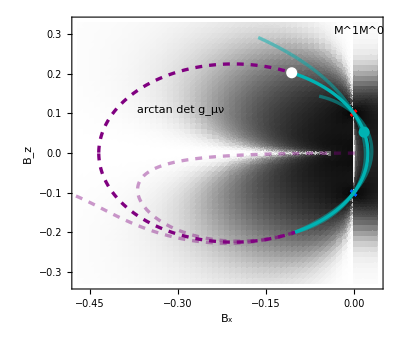

```mathematica
combinedGeod=PlotCombinedGeodCart[sol1,sol2,timeSwitch1,1,
{{sol1p,1,timeSwitch1p,{geodColor,Opacity[0.5]}},
{sol2p,2,timeSwitch2p,{geodColor,Opacity[0.5]}},
{sol1m,1,timeSwitch1m,{geodColor,Opacity[0.5]}},
{sol2m,2,timeSwitch2m,{geodColor,Opacity[0.5]}},
{solBottom,1.5,{MyViolet,Dashed}},
{solBottomP,0.4419,{MyViolet,Dashed,Opacity[0.4]}},
{solBottomM,1.5,{MyViolet,Dashed,Opacity[0.4]}},
{solUpper,1.5,{MyViolet,Dashed}}
}]
```